Visualizing Weight Learning in LeNet

Sorensen, Hikari

Alessandrini, Giulio

Harvard University

Most representative image

-Graphics-	`

Abstract

GOAL OF THE PROJECT: Examine the change in weights in LeNet over the training process.

SUMMARY OF WORK: LeNet was trained on MNIST and CIFAR-10, with weights and gradients saved at checkpoints along the training process. The weights and gradients were then visualized as images, upon which image difference and entropy analysis was conducted. The convolved images after training were also found, creating a visualization of the feature set upon which the weights were acting.

RESULTS AND FUTURE  WORK: 

Important results:
	- MNIST is a sufficiently simple dataset that filters undergo very little change from randomness; most of the learning is in the linear 	layers. That is, logistic regression is sufficient to achieve high accuracy on MNIST digit classification, and the convolutional layers 	serve primarily as a way to compress image information efficiently.

	- Training on CIFAR-10 results in filter learning. In this case, the random initializations of the filter weights have small magnitudes, 	which increase over training. This can be interpreted as maximizing image entropy of filters over the training process.

Future work:
	- Train sets of neural networks with different combinations of frozen layers, using different datasets and different network 		architectures. 
	
	- Create dynamic visualizations that update alongside network training, so that weight updates can be seen in real time. 
	
	- Try this kind of visualization for RNNs.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

## MNIST

### Imports

### Layer 1 filter images

#### Scaled to net weights

```mathematica
l1MNISTScaled = getL1MNISTImagesScaled[batchWeightsL1];
Column[l1MNISTScaled]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

### Layer 4 filter images

#### Scaled to net weights

```mathematica
l4MNISTScaled = getL4MNISTImagesScaled[batchWeightsL4];
Column[l4MNISTScaled]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

### Layer 8 filter images

#### Scaled to net weights

```mathematica
l8MNISTScaled = getL8MNISTImagesScaled[batchWeightsL8];
Column[l8MNISTScaled[[{1,Length[batchWeightsL8]}]]]
```

-Graphics-
-Graphics-

### Batch filter image entropy, layer 1

#### Image entropy plot function

```mathematica
plotBatchEntropyMNISTL1[batchImages_]:= Module[
	{dims = Dimensions[batchImages]},
	Show@
	ListPlot@
		Table[{i,
			Mean@
				Table[
					ImageMeasurements[batchImages[[i, j]], "Entropy"],
					{j, 1, dims[[2]]}
				]},
			{i, dims[[1]]}
		]
	]
```

#### Image entropy plots

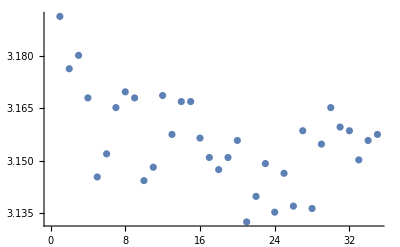
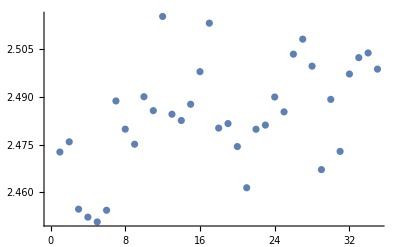
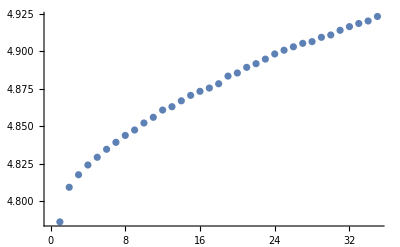

```mathematica
Table[plotBatchEntropyMNISTL1[Normal[images]],{images,{l1MNISTScaled,l4MNISTScaled,l8MNISTScaled}}]
```

### Convolved training images

```mathematica
convSampleValues = {7,0,2,3,3,5,2,5,2,0}
```

{7,0,2,3,3,5,2,5,2,0}

#### Convolution 1

```mathematica
conv1 ={{-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}}
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

#### Ramp 1 - negative weights go to 0

```mathematica
conv2 ={{-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}}
```

#### Pooling 1

```mathematica
conv3={{-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}}
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

#### Convolution 2 - each filter in first convolution gets convolved into 50 filters

```mathematica
conv4  ={{-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}}
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

#### Pooling 2 - reduce to 4x4 image

```mathematica
conv6 ={{-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}}
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

#### Flatten layer - flattens all 50 4x4 images of each training example into an 800-length feature vector

#### Feature vector function

```mathematica
featureVec[trainingPoint_] := 
	Return[
		Map[
			Colorize[
				Image[
					Rescale[#, MinMax[logAllW4W], {0, 1}],
					Interleaving -> False, 
					Magnification -> 5
				],
			ColorFunctionScaling -> False
		]&,
		{{Flatten[
			Table[
				out, 
				{out, netTable[[6]][trainingPoint[[1]]]}
			]
		]}}
		]
	];
```

#### Feature vector images

```mathematica
randomSampleTrain = RandomSample[trainingData,10]
```

{-Graphics-→9,-Graphics-→0,-Graphics-→7,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→6,-Graphics-→1,-Graphics-→9,-Graphics-→2}

```mathematica
Column[Table[featureVec[data],{data,randomSampleTrain}]]
```

{-Graphics-}
{-Graphics-}
{-Graphics-}
{-Graphics-}
{-Graphics-}
{-Graphics-}
{-Graphics-}
{-Graphics-}
{-Graphics-}
{-Graphics-}

```mathematica
Column[Table[featureVec[data],{data,set0[[1;;5]]}]]
```

{-Graphics-}
{-Graphics-}
{-Graphics-}
{-Graphics-}
{-Graphics-}

## CIFAR-10

### Imports

#### Net imports

```mathematica
filepath = "/Users/hikarisorensen/Dropbox/00_Pika/WSS_17/CIFAR_AWS/CIFAR_AWS/";
checkpointsPath = FileNameJoin[{filepath, "checkpoints"}];
cmPath = FileNameJoin[{filepath, "classifier_measurements"}];
logsPath = FileNameJoin[{filepath, "training_logs"}];
```

```mathematica
int := IntegerString[i];
netNames = Table[ Symbol[ "net" <> int ], {i, 0, 10}];
netPaths = Table[ FileNameJoin[{checkpointsPath, "net" <> int, "net" <> int <> ".wlnet"}], {i, 0, 10}];
```

```mathematica
net0 = Import[netPaths[[1]]];
net1 = Import[netPaths[[2]]];
net2 = Import[netPaths[[3]]];
net3 = Import[netPaths[[4]]];
net4 = Import[netPaths[[5]]];
(*net5 = Import[netPaths[[6]]];
net6 = Import[netPaths[[7]]];
net7 = Import[netPaths[[8]]];
net8 = Import[netPaths[[9]]];
net9 = Import[netPaths[[10]]];
net10 = Import[netPaths[[11]]];*)
```

Import::wlcorr: File is corrupt or is not a WLNet file.

```mathematica
.
```

```mathematica
allWeights = Table[Table[NetExtract[net, {i, "Weights"}],{net, {net0,net1,net2,net3,net4}}],{i,{1,4,8,10}}];
```

```mathematica
Position[allWeights,_?(#<-1&)]
```

{{1,5,6,3,3,4},{2,5,8,14,5,5},{2,5,10,14,5,5},{2,5,15,16,2,5},{2,5,16,14,3,5},{2,5,35,20,1,5},{2,5,42,6,3,2},{2,5,42,16,4,5},{2,5,44,19,3,1}}

```mathematica
Max[allWeights]
```

1.10932

```mathematica
Position[allWeights,_?(#>1&)]
```

{{2,5,2,9,5,1},{2,5,14,10,5,4},{2,5,44,9,4,3}}

```mathematica
Dimensions@allWeights
```

{4,5}

```mathematica
Min[allWeights]
```

-1.20802

#### Classifier measurements imports

```mathematica
cmPaths = 
	Table[
		FileNameJoin[{cmPath, "net" <> int, "net" <> int <> ".mx"}], 
	{i, 0, 10}];
```

```mathematica
cm0 = Import[cmPaths[[1]]];
cm1 = Import[cmPaths[[2]]];
cm2 = Import[cmPaths[[3]]];
cm3 = Import[cmPaths[[4]]];
cm4 = Import[cmPaths[[5]]];
(*cm5 = Import[cmPaths[[6]]];
cm6 = Import[cmPaths[[7]]];
cm7 = Import[cmPaths[[8]]];
cm8 = Import[cmPaths[[9]]];
cm9 = Import[cmPaths[[10]]];
cm10 = Import[cmPaths[[11]]];*)
```

### Net descriptions

Net 0: No frozen layers.
cm0["Accuracy"]
0.6968

Net 1: Freeze both conv. layers.
cm1["Accuracy"]
0.5564

Net 2: Freeze 1st conv. layer. 
cm2["Accuracy"]
0.6642

Net 3: Freeze 2nd conv. layer.
cm3["Accuracy"]
0.6366

Net 4: Freeze both linear layers.
cm4["Accuracy"]
0.5834

### Layer 1 filter images

#### All nets: Scaled to net weights

```mathematica
Map[getL1RGBImagesScaled,{net0,net1,net2,net3,net4}]
```

```mathematica
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
```

### Layer 4 filter images

#### Net0: Scaled to net weights

```mathematica
getL4ImagesScaled[net0]
```

```mathematica
n0l4CIFARScaled ={{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}};
```

```mathematica
getL4ImagesScaled[net4]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

#### Net4: Scaled to net weights

```mathematica
n4l4CIFARScaled={{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}};
```

### Layer 8 filter images

#### Net0: Scaled to net weights

```mathematica
n0l8CIFARScaled = 
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}};
```

### Batch filter image entropy, layer 1

#### Image entropy plots

Net 0 -- No frozen layers.
  Net 1 -- Freeze both conv. layers.
  Net 2 -- Freeze 1 st conv. layer. 
  Net 3 -- Freeze 2 nd conv. layer.
  Net 4 -- Freeze both linear layers.

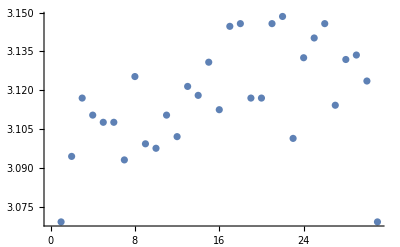
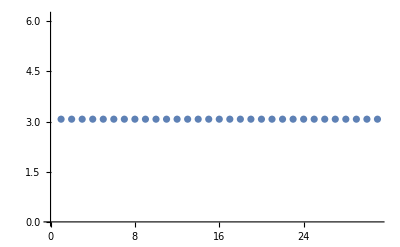
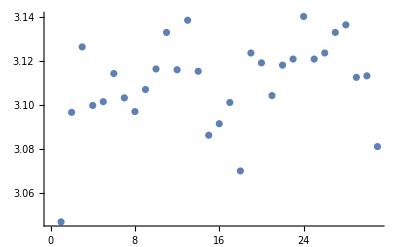
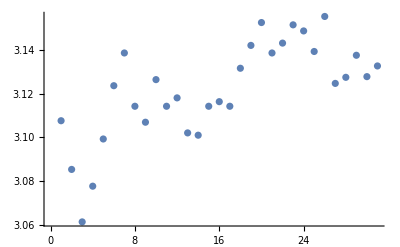
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[plotBatchEntropyL1[i],{i,0,4}]
```

### Batch filter image entropy, layer 4

#### Plots

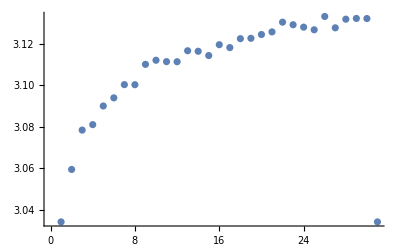
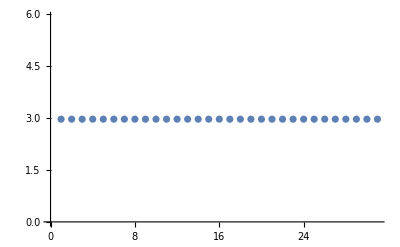
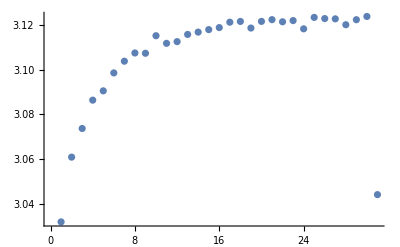
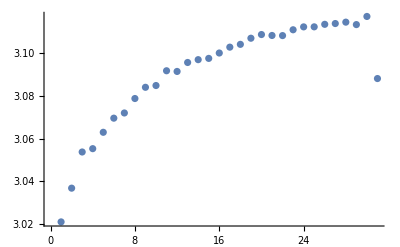
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[plotBatchEntropyL4[i],{i,0,4}]
```

#### 3D Entropy visualization as a function of epochs and layer 4 filters

```mathematica
ListPlot3D[Flatten[Table[{i,j,Mean@Table[ImageMeasurements[net0BatchImagesL4Scaled[[i,j,k]],"Entropy"],{k,1,20}]},{i,30},{j,1,50}],1], InterpolationOrder->20,Mesh -> None]
```

-Graphics3D-

#### Cumulative difference in layer 4 filters from first to last epoch

```mathematica
ColorNegate[MapThread[ImageDifference, {net0BatchImagesL4[[1]],net0BatchImagesL4[[30]]},2]]
```

```mathematica
cumuDiff = {{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
```

### Batch filter image entropy, layer 8

#### Plot function

```mathematica
plotBatchEntropyL8[netNum_]:= Module[
	{scaledImages = Table[getL8ImagesScaled[net], {net, getBatches[netNum]}]},
	dims = Dimensions[scaledImages];
	Show@
	ListPlot@
		Table[{i,
			Mean@
				Table[
					ImageMeasurements[scaledImages[[i, j]], "Entropy"],
					{j, 1, dims[[2]]}
				]},
			{i, dims[[1]]}
		]
	]
```

#### Plots

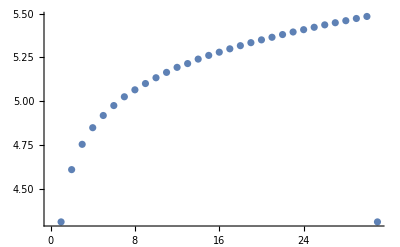
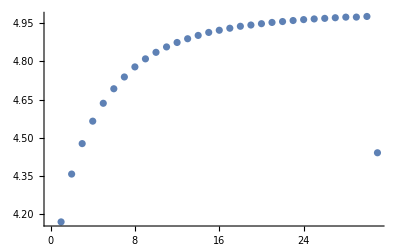
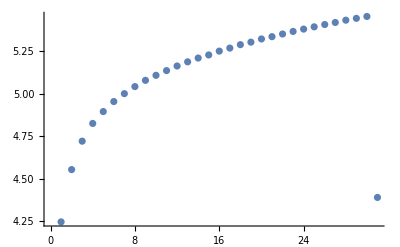
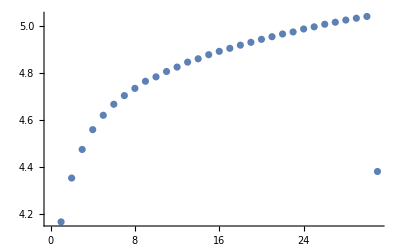
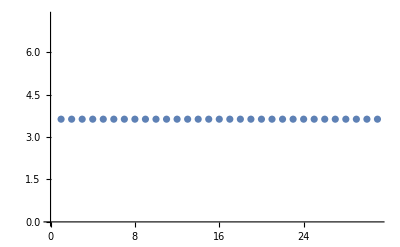

```mathematica
Table[plotBatchEntropyL8[i],{i,0,4}]
```

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail

Studying the weights at regular intervals over the training process of LeNet on MNIST revealed that the convolutional filters undergo little to no change over the course of training. Indeed, freezing the convolutional layers (preventing their weights from changing after their initial random initialization) in LeNet results in an accuracy loss of approx. 4% on an identically initialized, unfrozen net with accuracy 96%. That is, freezing the convolutional layers on a network that would have otherwise achieved 96% accuracy reduces the accuracy to 92%. 
	This suggests that most of the information discriminating between digits can be captured in the linear layers, and thus that the MNIST dataset is so structurally simple that it can be effectively learned with logistic regression. 
	
The CIFAR-10 dataset, however, is apparently substantially more complex. Here, the filters do show signs of learning-- that is, their weights do change substantially over the course of training. Moreover, freezing the convolutional layers reduces accuracy dramatically, from an unfrozen accuracy of 69.68% to 55.65%, approximately a 20% reduction in accuracy. 
	

In general, the extent to which layers undergo learning can be seen by examining the average image entropy of filter images over the course of training. This is a way of measuring the extent to which filters become discriminative of particular features, by amplifying the magnitudes of filter weights. That is, higher-entropy filter images depict “better learned” filters, and in particular, depict filters that can detect specific structures of images that prove predictive of the image class.
	When learning particular datasets, we can identify the layers at which the most learning occurs by plotting the trend in average filter image entropy at a particular layer. 
	The dominance of the linear layers in learning MNIST is clear when considering the filter entropy plots:

{-Graphics-,-Graphics-,-Graphics-}

The above plots show the average filter entropy as a function of progressive regular training intervals (every 3 epochs) over the course of training, for the 1st convolutional layer, 2nd convolutional layer, and 1st linear layer, respectively. We can clearly see that the convolutional layers have an approximately random progression of filter entropies over the course of training, while the average image entropy of the images of the weight matrices of the 1st linear layer increases monotonically. Moreover, paying attention to the scales reveals that overall entropy is much higher in the linear layer. Indeed, it is only in the linear layer that the weights become consistently amplified in magnitude and thus more discriminative of classes.

On the other hand, we see more involvement in the learning process of the convolutional layers when training on CIFAR-10. The following plots show, like for MNIST, the average filter entropy as a function of progressive regular training intervals over the course of training, for the same respective layers. The filters in the 2nd convolutional layer when training on CIFAR-10 follow a clear upward trajectory. Moreover, while filter entropy decreases substantially on average between the 1st and 2nd convolutional layers when training on MNIST, paying attention to the plot scales shows that this major decrease does not occur when training on CIFAR-10.

One idea that could be drawn is that the extent to which layers learn is a function of the layer itself. And indeed, this seems to be largely the case. For example, consider the following average entropy values over the training process in training LeNet on CIFAR-10, with various layers frozen:

Both convolutional layers frozen:

First convolutional layer frozen:

Second convolutional layer frozen:

First linear layer frozen:

And indeed, it does not appear that, at least for CIFAR-10, other layers will “compensate” for learning that is lost at any frozen layer.

Code

Link to the GitHub

## MNIST

### Imports

### Layer 1 filter images

#### Scaled to layer weights

```mathematica
l1MNISTUnscaled = getL1MNISTImages[batchWeightsL1];
Column[l1MNISTUnscaled]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

#### Scaled to net weights

```mathematica
l1MNISTScaled = getL1MNISTImagesScaled[batchWeightsL1];
Column[l1MNISTScaled]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

### Layer 4 filter images

#### Scaled to layer weights

```mathematica
l4MNISTUnscaled = getL4MNISTImages[batchWeightsL4];
Column[l4MNISTUnscaled]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

#### Scaled to net weights

```mathematica
l4MNISTScaled = getL4MNISTImagesScaled[batchWeightsL4];
Column[l4MNISTScaled]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

### Layer 8 filter images

#### Scaled to layer weights

```mathematica
l8MNISTUnscaled = getL8MNISTImages[batchWeightsL8];
Column[l8MNISTUnscaled[[{1,Length[batchWeightsL8]}]]]
```

-Graphics-
-Graphics-

#### Scaled to net weights

```mathematica
l8MNISTScaled = getL8MNISTImagesScaled[batchWeightsL8];
Column[l8MNISTScaled[[{1,Length[batchWeightsL8]}]]]
```

-Graphics-
-Graphics-

### Batch filter image entropy, layer 1

#### Image entropy plot function

```mathematica
plotBatchEntropyMNISTL1[batchImages_]:= Module[
	{dims = Dimensions[batchImages]},
	Show@
	ListPlot@
		Table[{i,
			Mean@
				Table[
					ImageMeasurements[batchImages[[i, j]], "Entropy"],
					{j, 1, dims[[2]]}
				]},
			{i, dims[[1]]}
		]
	]
```

#### Image entropy plots

```mathematica
Table[plotBatchEntropyMNISTL1[Normal[images]],{images,{l1MNISTScaled,l4MNISTScaled,l8MNISTScaled}}]
```

{-Graphics-,-Graphics-,-Graphics-}

### Convolved training images

```mathematica
convSampleValues = {7,0,2,3,3,5,2,5,2,0}
```

{7,0,2,3,3,5,2,5,2,0}

#### Convolution 1

```mathematica
conv1 ={{-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}}
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

#### Ramp 1 - negative weights go to 0

```mathematica
conv2 ={{-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}}
```

#### Pooling 1

```mathematica
conv3={{-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}}
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

#### Convolution 2 - each filter in first convolution gets convolved into 50 filters

```mathematica
conv4  ={{-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}}
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

#### Pooling 2 - reduce to 4x4 image

```mathematica
conv6 ={{-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}, {-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}}
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

#### Flatten layer - flattens all 50 4x4 images of each training example into an 800-length feature vector

#### Feature vector function

```mathematica
featureVec[trainingPoint_] := 
	Return[
		Map[
			Colorize[
				Image[
					Rescale[#, MinMax[logAllW4W], {0, 1}],
					Interleaving -> False, 
					Magnification -> 5
				],
			ColorFunctionScaling -> False
		]&,
		{{Flatten[
			Table[
				out, 
				{out, netTable[[6]][trainingPoint[[1]]]}
			]
		]}}
		]
	];
```

#### Feature vector images

```mathematica
randomSampleTrain = RandomSample[trainingData,10]
```

{-Graphics-→9,-Graphics-→0,-Graphics-→7,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→6,-Graphics-→1,-Graphics-→9,-Graphics-→2}

```mathematica
Column[Table[featureVec[data],{data,randomSampleTrain}]]
```

{-Graphics-}
{-Graphics-}
{-Graphics-}
{-Graphics-}
{-Graphics-}
{-Graphics-}
{-Graphics-}
{-Graphics-}
{-Graphics-}
{-Graphics-}

```mathematica
Column[Table[featureVec[data],{data,set0[[1;;5]]}]]
```

{-Graphics-}
{-Graphics-}
{-Graphics-}
{-Graphics-}
{-Graphics-}

## CIFAR-10

### Imports

#### Net imports

```mathematica
filepath = "/Users/hikarisorensen/Dropbox/00_Pika/WSS_17/CIFAR_AWS/CIFAR_AWS/";
checkpointsPath = FileNameJoin[{filepath, "checkpoints"}];
cmPath = FileNameJoin[{filepath, "classifier_measurements"}];
logsPath = FileNameJoin[{filepath, "training_logs"}];
```

```mathematica
int := IntegerString[i];
netNames = Table[ Symbol[ "net" <> int ], {i, 0, 10}];
netPaths = Table[ FileNameJoin[{checkpointsPath, "net" <> int, "net" <> int <> ".wlnet"}], {i, 0, 10}];
```

```mathematica
net0 = Import[netPaths[[1]]];
net1 = Import[netPaths[[2]]];
net2 = Import[netPaths[[3]]];
net3 = Import[netPaths[[4]]];
net4 = Import[netPaths[[5]]];
(*net5 = Import[netPaths[[6]]];
net6 = Import[netPaths[[7]]];
net7 = Import[netPaths[[8]]];
net8 = Import[netPaths[[9]]];
net9 = Import[netPaths[[10]]];
net10 = Import[netPaths[[11]]];*)
```

Import::wlcorr: File is corrupt or is not a WLNet file.

```mathematica
.
```

```mathematica
allWeights = Table[Table[NetExtract[net, {i, "Weights"}],{net, {net0,net1,net2,net3,net4}}],{i,{1,4,8,10}}];
```

```mathematica
Position[allWeights,_?(#<-1&)]
```

{{1,5,6,3,3,4},{2,5,8,14,5,5},{2,5,10,14,5,5},{2,5,15,16,2,5},{2,5,16,14,3,5},{2,5,35,20,1,5},{2,5,42,6,3,2},{2,5,42,16,4,5},{2,5,44,19,3,1}}

```mathematica
Max[allWeights]
```

1.10932

```mathematica
Position[allWeights,_?(#>1&)]
```

{{2,5,2,9,5,1},{2,5,14,10,5,4},{2,5,44,9,4,3}}

```mathematica
Dimensions@allWeights
```

{4,5}

```mathematica
Min[allWeights]
```

-1.20802

#### Classifier measurements imports

```mathematica
cmPaths = 
	Table[
		FileNameJoin[{cmPath, "net" <> int, "net" <> int <> ".mx"}], 
	{i, 0, 10}];
```

```mathematica
cm0 = Import[cmPaths[[1]]];
cm1 = Import[cmPaths[[2]]];
cm2 = Import[cmPaths[[3]]];
cm3 = Import[cmPaths[[4]]];
cm4 = Import[cmPaths[[5]]];
(*cm5 = Import[cmPaths[[6]]];
cm6 = Import[cmPaths[[7]]];
cm7 = Import[cmPaths[[8]]];
cm8 = Import[cmPaths[[9]]];
cm9 = Import[cmPaths[[10]]];
cm10 = Import[cmPaths[[11]]];*)
```

### Net descriptions

Net 0: No frozen layers.
cm0["Accuracy"]
0.6968

Net 1: Freeze both conv. layers.
cm1["Accuracy"]
0.5564

Net 2: Freeze 1st conv. layer. 
cm2["Accuracy"]
0.6642

Net 3: Freeze 2nd conv. layer.
cm3["Accuracy"]
0.6366

Net 4: Freeze both linear layers.
cm4["Accuracy"]
0.5834

### Layer 1 filter images

#### All nets: Scaled to layer weights

```mathematica
Map[getL1RGBImages,{net0,net1,net2,net3,net4}]
```

```mathematica
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
```

#### All nets: Scaled to net weights

```mathematica
Map[getL1RGBImagesScaled,{net0,net1,net2,net3,net4}]
```

```mathematica
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
```

### Layer 4 filter images

#### Get images function for layer 4

```mathematica
getL4Images[net_] := Module[
	{weights = NetExtract[net, {4, "Weights"}]},
	Return[
		Table[ 
			Map[
				Colorize[
					Image[
						Rescale[#, MinMax[weights], {0, 1}],
						Interleaving -> False, 
						ImageSize -> 20
					],
				ColorFunctionScaling -> False
				]&,
				weights[[i]]
			],
			{i, Length[weights]}
		]
	]
];
```

```mathematica
getL4ImagesScaled[net_] := Module[
	{weights = NetExtract[net, {4, "Weights"}]},
	Return[
		Table[ 
			Map[
				Colorize[
					Image[
						Rescale[#, MinMax[allWeights], {0, 1}],
						Interleaving -> False, 
						ImageSize -> 20
					],
				ColorFunctionScaling -> False
				]&,
				weights[[i]]
			],
			{i, Length[weights]}
		]
	]
];
```

#### Net0: Scaled to layer weights

```mathematica
getL4Images[net0]
```

```mathematica
n0l4CIFARUnscaled ={{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}};
```

#### Net0: Scaled to net weights

```mathematica
getL4ImagesScaled[net0]
```

```mathematica
n0l4CIFARScaled ={{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}};
```

```mathematica
getL4ImagesScaled[net4]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

#### Net4: Scaled to net weights

```mathematica
n4l4CIFARScaled={{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}};
```

### Layer 8 filter images

#### Get images function for layer 8

```mathematica
getL8Images[net_] := Module[
	{weights = NetExtract[net, {8, "Weights"}]},
	Return[
		Table[ 
			Map[
				Colorize[
					Image[
						Rescale[#, MinMax[weights], {0, 1}],
						Interleaving -> False, 
						Magnification -> 1
					],
				ColorFunctionScaling -> False
				]&,
				weights[[i]]
			],
			{i, Length[weights]}
		]
	]
];
```

```mathematica
getL8ImagesScaled[net_] := Module[
	{weights = NetExtract[net, {8, "Weights"}]},
	Return[
			Map[
				Colorize[
					Image[
						Rescale[#, MinMax[allWeights], {0, 1}],
						Interleaving -> False, 
						Magnification -> 1
					],
				ColorFunctionScaling -> False
				]&,
				{weights}
			]
		]
];
```

#### Net0: Scaled to net weights

```mathematica
n0l8CIFARScaled = 
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}};
```

### Batch filter image entropy, layer 1

#### Image entropy plot function

```mathematica
plotBatchEntropyL1[netNum_]:= Module[
	{scaledImages = Table[getL1RGBImagesScaled[net], {net, getBatches[netNum]}]},
	dims = Dimensions[scaledImages];
	Show@
	ListPlot@
		Table[{i,
			Mean@
				Table[
					ImageMeasurements[scaledImages[[i, j]], "Entropy"],
					{j, 1, dims[[2]]}
				]},
			{i, dims[[1]]}
		]
	]
```

#### Image entropy plots

Net 0 -- No frozen layers.
  Net 1 -- Freeze both conv. layers.
  Net 2 -- Freeze 1 st conv. layer. 
  Net 3 -- Freeze 2 nd conv. layer.
  Net 4 -- Freeze both linear layers.

```mathematica
Table[plotBatchEntropyL1[i],{i,0,4}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Filter diff layer 1 plots

```mathematica
net0BatchDiff = getBatchDiff[net0BatchImages];
```

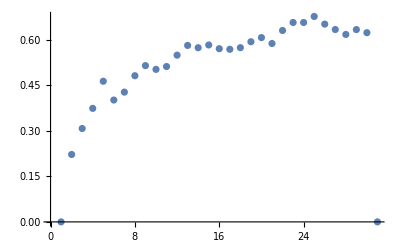

```mathematica
plotBatchDiff[net0BatchDiff]
```

```mathematica
Table[getL1RGBImages[net],{net,batchesNet1}]
```

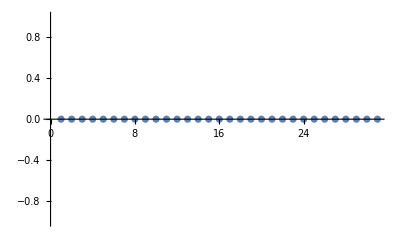

```mathematica
plotBatchDiff[getBatchDiff[Table[getL1RGBImages[net],{net,batchesNet1}]]]
```

```mathematica
plotBatchDiff[getBatchDiff[Table[getL1RGBImages[net],{net,batchesNet2}]]]
```

-Graphics-

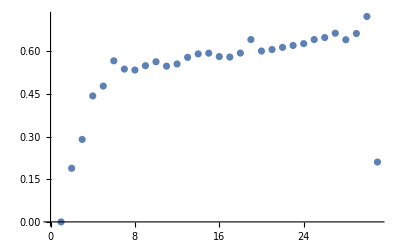

```mathematica
plotBatchDiff[getBatchDiff[Table[getL1RGBImages[net],{net,batchesNet3}]]]
```

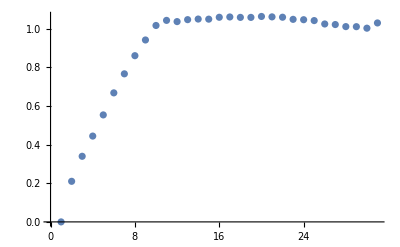

```mathematica
plotBatchDiff[getBatchDiff[Table[getL1RGBImages[net],{net,batchesNet4}]]]
```

### Batch weight images, layer 4

```mathematica
Dimensions@batchWeights0L4
```

{31,50,20,5,5}

```mathematica
net0BatchImagesL4 = Table[getL4Images[net],{net,batchesNet0}];
```

```mathematica
net0BatchImagesL4Scaled = Table[getL4ImagesScaled[net],{net,batchesNet0}];
```

```mathematica
Dimensions@net0BatchImagesL4
```

{31,50,20}

```mathematica
Table[ImageMeasurements[net0BatchImagesL4[[1,1,k]],"Entropy"],{k,1,5}]
```

{3.10797,3.21888,3.03159,3.16342,3.16342}

### Batch filter image entropy, layer 4

#### Plot function

```mathematica
plotBatchEntropyL4[netNum_]:= Module[
	{scaledImages = Table[getL4ImagesScaled[net], {net, getBatches[netNum]}]},
	dims = Dimensions[scaledImages];
	Show@
	ListPlot@
		Table[{i,
			Mean@Mean@
				Table[
					ImageMeasurements[scaledImages[[i, j, k]], "Entropy"],
					{k, 1, dims[[3]]},
					{j, 1, dims[[2]]}
				]},
			{i, dims[[1]]}
		]
	]
```

#### Plots

```mathematica
Table[plotBatchEntropyL4[i],{i,0,4}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### 3D Entropy visualization as a function of epochs and layer 4 filters

```mathematica
ListPlot3D[Flatten[Table[{i,j,Mean@Table[ImageMeasurements[net0BatchImagesL4Scaled[[i,j,k]],"Entropy"],{k,1,20}]},{i,30},{j,1,50}],1], InterpolationOrder->20,Mesh -> None]
```

-Graphics3D-

#### Cumulative difference in layer 4 filters from first to last epoch

```mathematica
ColorNegate[MapThread[ImageDifference, {net0BatchImagesL4[[1]],net0BatchImagesL4[[30]]},2]]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

### Batch filter image entropy, layer 8

#### Plot function

```mathematica
plotBatchEntropyL8[netNum_]:= Module[
	{scaledImages = Table[getL8ImagesScaled[net], {net, getBatches[netNum]}]},
	dims = Dimensions[scaledImages];
	Show@
	ListPlot@
		Table[{i,
			Mean@
				Table[
					ImageMeasurements[scaledImages[[i, j]], "Entropy"],
					{j, 1, dims[[2]]}
				]},
			{i, dims[[1]]}
		]
	]
```

#### Plots

```mathematica
Table[plotBatchEntropyL8[i],{i,0,4}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Written Content / Lesson Plans

Conclusions in Detail

All Visualizations

Data Sources Links/References

MNIST Dataset Documentation: http://yann.lecun.com/exdb/mnist/

CIFAR-10 Dataset Documentation: https://www.cs.toronto.edu/~kriz/cifar.html

Future Directions

Background Info Links/References

Wolfram Language Documentation: http://reference.wolfram.com/language/ref/

Keywords

Provide keywords as items

convolutional neural networks

MNIST

CIFAR-10

image classification

digit recognition

machine learning

Other

Date

Last Modified: Monday, July 03, 2017

```mathematica
"Add Timestamp"
```